# Boolean Algebra *will change it to sth more interesting*

Dali Lai

1. Combinational Circuit-logic gate

By combining different logic gates (AND, NAND, OR...etc.), the circuit can output the desired output while receiving a certain input. 
In programming, know as truth table (but more complicated). 

For example X or Y:

```mathematica
Grid[MapThread[Prepend,{Prepend[BooleanTable[x||y,{x},{y}],{"1","0"}],{"x/y","1","0"}}],Frame->All]
```

x/y | 1 | 0
1 | True | True
0 | True | False

```mathematica
(*I kinda hard coded the 1 and 0, any other way to do it ? Like how to make is count as binary from 00 to w/e many the cell there is ? i.e. 4 cells then it will be 00 01 10 11*)
```

To prove it, let’s simulate the logic gate OR with 2 inputs in SystemModeler

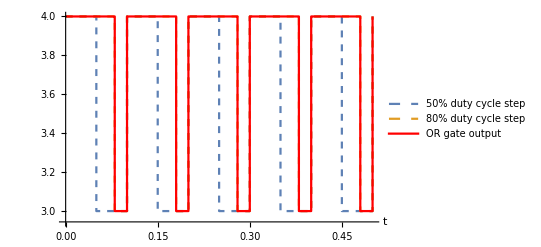

```mathematica
Show[SystemModelPlot[SystemModelSimulate[-Graphics-,{0,0.5}],{"pulse1.y","pulse2.y"},PlotStyle->Dashed,PlotLegends->{"50% duty cycle step","80% duty cycle step"},PlotStyle->Thick],SystemModelPlot[SystemModelSimulate[-Graphics-,{0,0.5}],{"orGate1.y"},PlotLegends->{"OR gate output"},PlotStyle->{Red,Thin}]]
```

2. Combinational Circuit-logic expression